```mathematica
(*ClearAll["Global`*"]*)
(* Plot the phase space potrait of the 1D phi4 problem *)
```

```mathematica
(* The EOMs are *)
(* time derivative of position *)
qdot[p_]:=p
qdot[p]
```

p

```mathematica
(* source term *)
Source[t_,A_,R_]:=A/R/Sqrt[Pi]*Exp[-t^2/R^2]
Source[t,A,R]
```

(A ⅇ^(-t^2/R^2))/(√π R)

```mathematica
(* time derivative of velocity *)
pdot[q_,S_]:=q(q^2-1)/2+S
pdot[q,S]
```

1/2 q (-1+q^2)+S

```mathematica
(* Has 3 "fixed points" if source strength below critical 1/3/Sqrt[3] *)
(* Has 1 "fixed point" if source strength above critical 1/3/Sqrt[3] *)
ARc=1/3/Sqrt[3]
(*q/.Solve[dotp[q,0,AR,1]==0,q]*)
```

1/(3 √3)

```mathematica
(* Write at t=0, S = A/√π R *)
fixed[S_]:=q/.Solve[pdot[q,S]==0,q]
f1D=fixed[0.1]
f1D[[1]]
```

{-1.08803,0.209149,0.878885}

-1.08803

```mathematica
(* List of fixed points in 2d phase space *)
fixed2D[S_]:=Table[{fixed[S][[n]],0},{n,1,3}]
fixed2D[0.1]
```

{{-1.08803,0},{0.209149,0},{0.878885,0}}

```mathematica
(* Source free case, separatrix in the qp phase space *)
P2sep[q_,S_]:=1/4q^4-1/2q^2+2*S q
P2sep[q,S]
```

-q^2/2+q^4/4+2 q S

```mathematica
(* function that maskes phase space potraits *)
Potrait[t_,A_,R_]:=Module[
{max,S,f1D,v,s,lf,lp,l,sep,q},
S = Source[t,A,R];
f1D=fixed[S];
max=2*Max[Abs[f1D]];
(* vector plot *)
v = VectorPlot[{qdot[p],pdot[q,S]},{q,-max,max},{p,-max,max},Axes->True,AxesLabel->{"q","p"}];
(* stream plot *)
s=StreamPlot[{qdot[p],pdot[q,S]},{q,-max,max},{p,-max,max},Axes->True,AxesLabel->{"q","p"},StreamStyle->Black];
(* mark fixed points *)
lf=ListPlot[fixed2D[S],PlotStyle->Directive[PointSize[0.03],Black]];
(* mark separatrix *)
sep={Re[Sqrt[P2sep[q,S]-P2sep[f1D[[1]],S]]],-Re[Sqrt[P2sep[q,S]-P2sep[f1D[[1]],S]]]};
If[S<ARc,sep=Flatten[Append[sep,{Re[Sqrt[P2sep[q,S]-P2sep[f1D[[3]],S]]],-Re[Sqrt[P2sep[q,S]-P2sep[f1D[[3]],S]]]}]],];
lp =Plot[sep,{q,-max,max},PlotStyle->Directive[Black,Thickness[0.008]]];
l=Show[lf,lp];
Return[{v,s,l}]
]
```

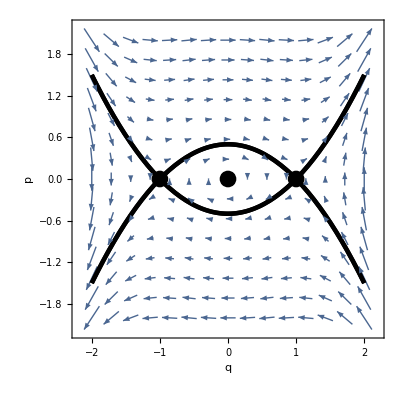

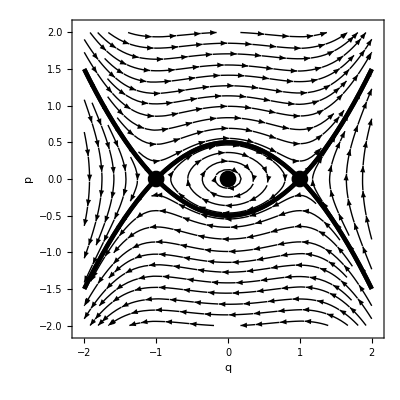

```mathematica
(* No source term *)
{v0,s0,l0}=Potrait[0,0,1];
Show[v0,l0,ImageSize->400,AspectRatio->1]
Show[s0,l0,ImageSize->400,AspectRatio->1]
```

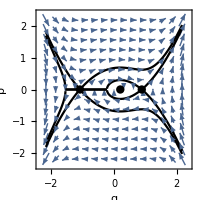

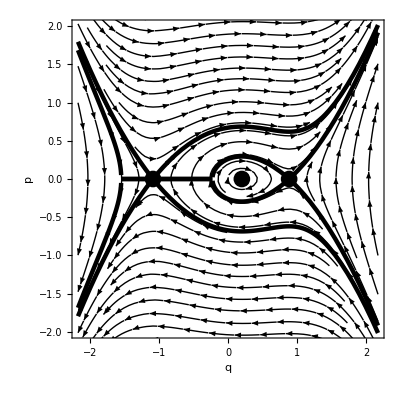

```mathematica
(* Small source term *)
{v1,s1,l1}=Potrait[0,0.5*ARc,1/Sqrt[Pi]];
Show[v1,l1,ImageSize->200,AspectRatio->1]
Show[s1,l1,ImageSize->400,AspectRatio->1,PlotRange->{-2,2}]
```

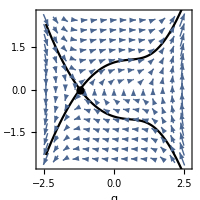

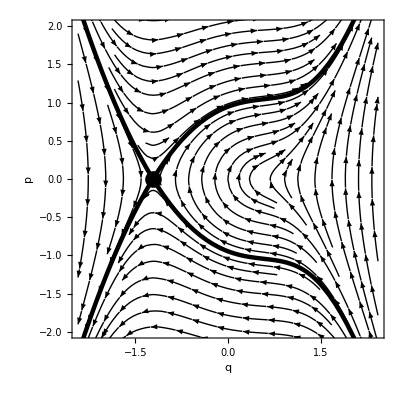

```mathematica
(* Large source term *)
{v2,s2,l2}=Potrait[0,1.5*ARc,1/Sqrt[Pi]];
Show[v2,l2,ImageSize->200,AspectRatio->1]
Show[s2,l2,ImageSize->400,AspectRatio->1,PlotRange->{-2,2}]
```

```mathematica
(*****************************************)
(* Delta function source term *)
(* Normalized light-horizon radius for islands boundary*)
Rbc[A_]:=2*ArcCosh[1/Sqrt[Abs[A]]]
Rbc[A]
```

2 ArcCosh[1/(√Abs[A])]

```mathematica
(* Normalized light-horizon radius for separatrix *)
Rsc[A_]:=2*ArcSinh[1/Sqrt[Abs[A]]]
Rsc[A]
```

2 ArcSinh[1/(√Abs[A])]

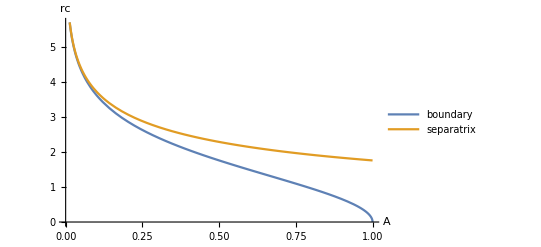

```mathematica
Plot[{Rbc[A],Rsc[A]},{A,0,1},PlotLegends->{"boundary","separatrix"},AxesLabel->{"A","rc"}]
```

```mathematica
(* Finite energy solutions, on island boundary *)
(* s>0: perturbative, s<0 nonperturbative *)
qbFinite[t_,A_,s_]:=Sign[A] Tanh[(Abs[t]+Sign[s]*Rbc[A])/2]
qbFinite[t,A,s]
```

Sign[A] Tanh[1/2 (Abs[t]+2 ArcCosh[1/(√Abs[A])] Sign[s])]

```mathematica
pbFinite[t_,A_,s_]:=Sign[A]*Sign[t]/2/Cosh[(Abs[t]+Sign[s]*Rbc[A])/2]^2
pbFinite[t,A,s]
```

1/2 Sech[1/2 (Abs[t]+2 ArcCosh[1/(√Abs[A])] Sign[s])]^2 Sign[A] Sign[t]

```mathematica
(* Finite energy solutions, on separatrix *)
qsFinite[t_,A_]:=-Sign[A]Coth[(Abs[t]+Rsc[A])/2]
qsFinite[t,A]
```

-Coth[1/2 (Abs[t]+2 ArcSinh[1/(√Abs[A])])] Sign[A]

```mathematica
psFinite[t_,A_]:=Sign[A]*Sign[t]/2/Sinh[(Abs[t]+Rsc[A])/2]^2
psFinite[t,A]
```

1/2 Csch[1/2 (Abs[t]+2 ArcSinh[1/(√Abs[A])])]^2 Sign[A] Sign[t]

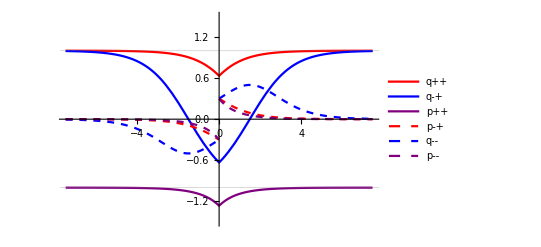

```mathematica
A0=0.6;(* should <1 *)
tmax = 5*Rbc[A0];
Plot[{qbFinite[t,A0,1],qbFinite[t,A0,-1],qsFinite[t,A0],pbFinite[t,A0,1],pbFinite[t,A0,-1],psFinite[t,A0]},{t,-tmax,tmax}, PlotStyle->{Red,Blue,Purple,Directive[Red,Dashed],Directive[Blue,Dashed],Directive[Purple,Dashed]}, PlotLegends->{"q++","q-+","p++","p-+","q--","p--"},GridLines->{None, {-1,1}},PlotRange->{-1.5,1.5}]
```

```mathematica
(* Plot finite energy solutions in phase space *)
PlotFinite[A_,tmax_]:=Module[
{ft, f0, q0, p0, al, fal, ar, far, as,fas,fp,},
(********************************)
(* Plot as function of t *)
ft = Plot[{qbFinite[t,A,1],qbFinite[t,A,-1],qsFinite[t,A]},{t,-tmax,tmax},PlotRange->{-2,2},PlotStyle->{Directive[Orange,Thickness[0.01]],Directive[Blue,Thickness[0.006]],Directive[Purple,Thickness[0.006]]},AxesLabel->{"t","q"}];
(********************************)
(* Parametric plot in phase space *)
f0=ParametricPlot[{{qbFinite[t,A,1],pbFinite[t,A,1]},{qbFinite[t,A,-1],pbFinite[t,A,-1]},{qsFinite[t,A],psFinite[t,A]}},{t,-tmax,tmax},PlotRange->All,PlotStyle->{Directive[Orange,Thickness[0.015]],Directive[Blue,Thickness[0.007]],Directive[Purple,Thickness[0.006]]},AxesLabel->{"q","p"}];
(* draw left kick arrow *)
q0 = qbFinite[0,A,-1];
p0 =pbFinite[-0.01,A,-1];
al = {Arrowheads[Large],Arrow[{{q0,p0},{q0,p0+A}}]};
fal=Graphics[{Thickness[0.006],Blue,al}];
(* draw lright kick arrow *)
q0 = qbFinite[0,A,1];
p0 =pbFinite[-0.01,A,1];
ar= {Arrowheads[Large],Arrow[{{q0,p0},{q0,p0+A}}]};
far=Graphics[{Thickness[0.006],Orange,ar}];
(* draw separatrix kick arrow *)
q0 = qsFinite[0,A];
p0 =psFinite[-0.01,A];
as= {Arrowheads[Large],Arrow[{{q0,p0},{q0,p0+A}}]};
fas=Graphics[{Thickness[0.006],Purple,as}];
(* Show both on same plot *)
fp = Show[f0,fal, far,fas];
Return[{ft,fp}]
]
```

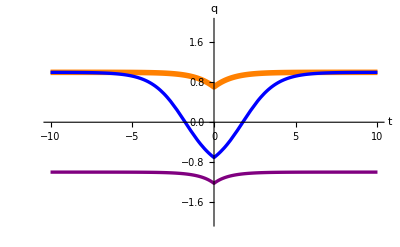

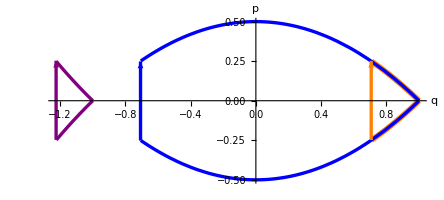

```mathematica
A0=0.5;
tmax0=10;
{ftc,fpc}=PlotFinite[A0,tmax0];
Show[ftc]
Show[fpc]
```

```mathematica
(* Solution of ODE with delta function souce *)
(* Kick by dP=A for t>0 *)
Delta[q0_, p0_,A_,tmax_,color_,tk_]:=Module[
{sn, sp,q,fl,fr,ft,f0,a,fa,fp,t},
(* solution without kick for t<0 *)
sn=NDSolve[{q''[t]==q[t](q[t]^2-1)/2,q[0]==q0,q'[0]==p0},q,{t,-tmax,0}];
(* solution without kick for t<0 *)
sp=NDSolve[{q''[t]==q[t](q[t]^2-1)/2,q[0]==q0,q'[0]==p0+A},q,{t,0,tmax}];
(********************************)
(* Plot as function of t *)
fl = Plot[Evaluate[q[t]/.sn],{t,-tmax,0},PlotRange->{{-tmax,tmax},{-2,2}},PlotStyle->Directive[color,Thickness[tk]],AxesLabel->{"t","q"}];
fr = Plot[Evaluate[q[t]/.sp],{t,0,tmax},PlotRange->{{-tmax,tmax},{-2,2}},PlotStyle->Directive[color,Thickness[tk]],AxesLabel->{"t","q"}];
ft = Show[fl,fr];
(********************************)
(* Parametric plot in phase space *)
f0=ParametricPlot[{Evaluate[{q[-t],q'[-t]}/.sn],Evaluate[{q[t],q'[t]}/.sp]},{t,0,tmax},PlotRange->{{-1.5,1.5},{-1.5,1.5}},PlotStyle->Directive[color,Thickness[tk]],AxesLabel->{"q","p"}];
(* draw kick arroe *)
a = {Arrowheads[Large],Arrow[{{q0,p0},{q0,p0+A}}]};
fa=Graphics[{Thickness[tk],color,a}];
(* Show both on same plot *)
fp = Show[f0,fa];
Return[{ft,fp}]
]
```

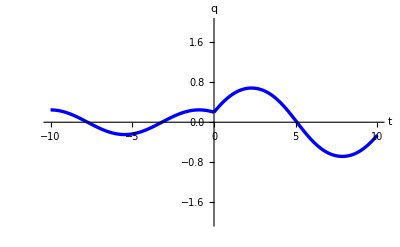

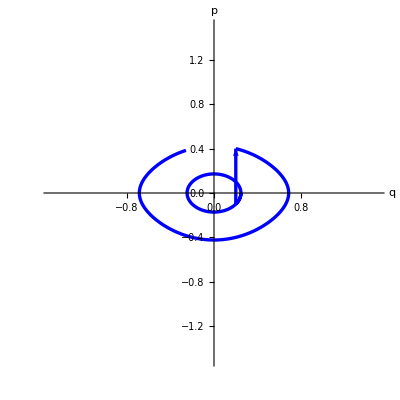

```mathematica
q00=0.2;
p00=-0.1;
{ft,fp}=Delta[q00,p00,A0,tmax0,Blue,0.006];
Show[ft]
Show[fp]
```

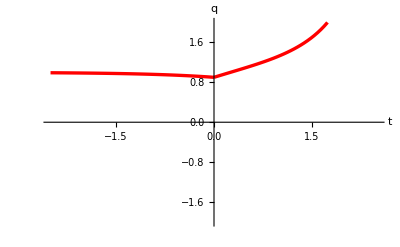

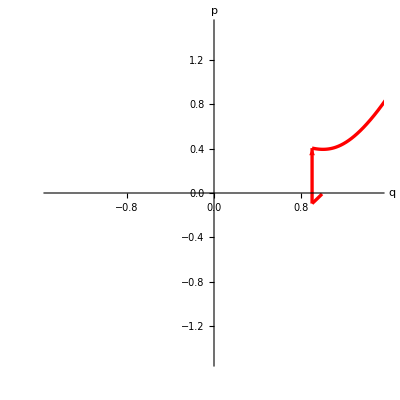

```mathematica
q01=0.9;
p01=-0.095;
{ft1,fp1}=Delta[q01,p01,A0,tmax0/4,Red,0.006];
Show[ft1]
Show[fp1]
```

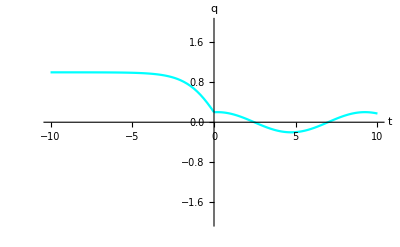

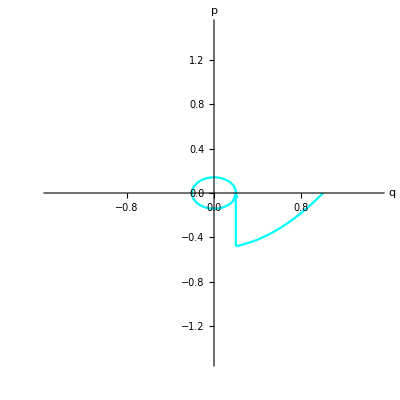

```mathematica
q02=0.2;
p02=-0.48;
{ft2,fp2}=Delta[q02,p02,A0,tmax0,Cyan,0.004];
Show[ft2]
Show[fp2]
```

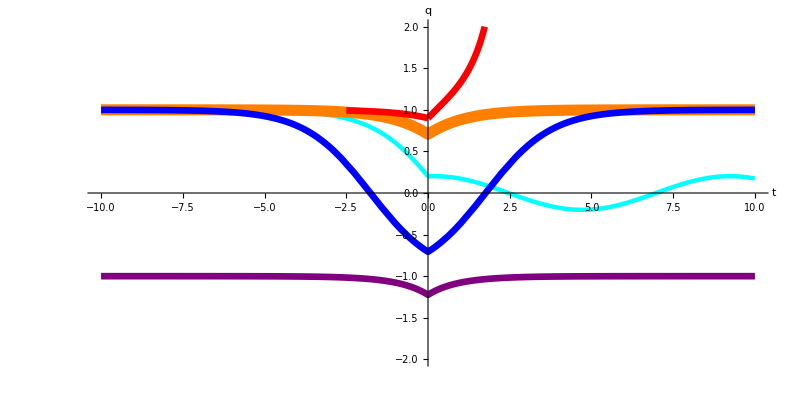

```mathematica
Show[ft2,ftc,ft1,ImageSize->800,AspectRatio->1/2]
```

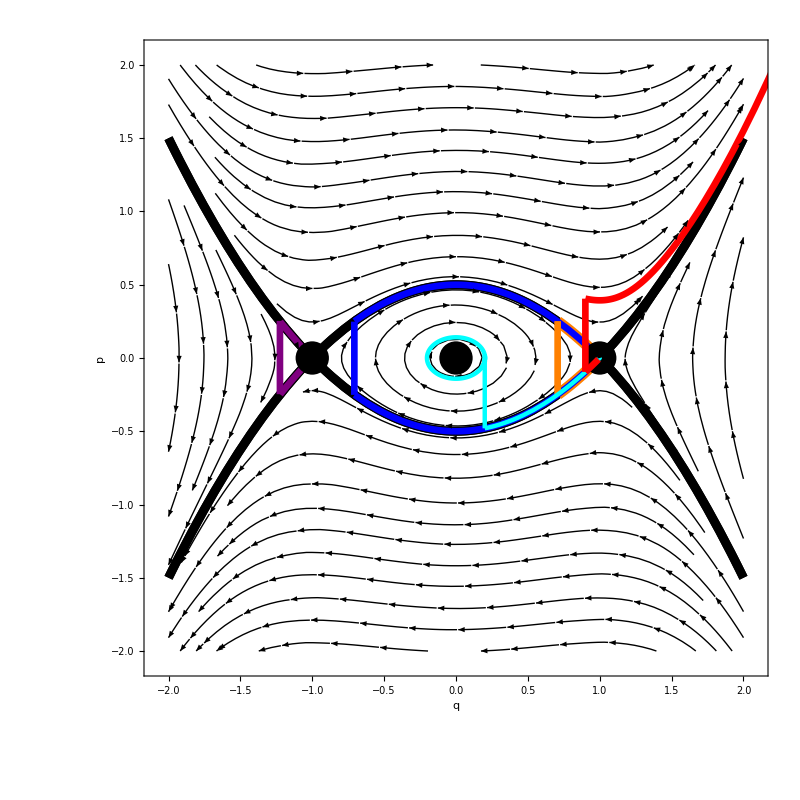

```mathematica
Show[s0,l0,fpc,fp2,fp1,ImageSize->800,AspectRatio->1]
```

```mathematica
(* source term at origin *)
S0[R_,A_]:=A/R/Sqrt[Pi]
S0[R,A]
```

A/(√π R)

```mathematica
(* Separation between separatrix and island left boundary *)
(* For large R and small S0 *)
dqLargeR[s_]:=2*(s+Sqrt[s])
dqLargeR[s]
```

2 (√s+s)

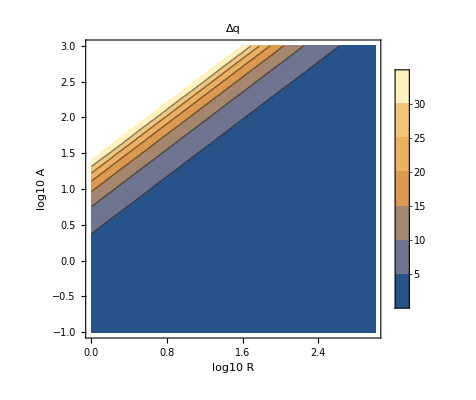

```mathematica
ContourPlot[dqLargeR[S0[10^logR,10^logA]],{logR,0,3},{logA,-1,3},AxesLabel->{"log10 R", "log10 A"},PlotLabel->"Δq",PlotLegends->Automatic]
```

```mathematica
(* Solution to dq = dqLargeR[s] *)
d2S[dq_]:=(dq+1-Sqrt[1+2dq])/2
d2S[dq]
```

1/2 (1+dq-√(1+2 dq))

```mathematica
FullSimplify[dqLargeR[d2S[Pi/4]]]
```

π/4

```mathematica
(* For small R, the gap is ~A *)
(* A as function of R, for which the small R and large R gap dq equals *)
ASeL[R_]:=R*Sqrt[Pi]/(R*Sqrt[Pi]/2-1)^2
ASeL[R]
```

(√π R)/(-1+(√π R)/2)^2

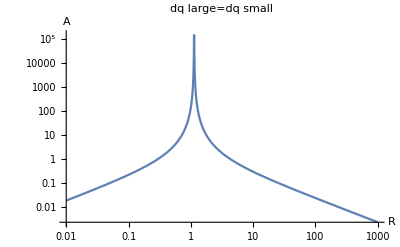

```mathematica
LogLogPlot[ASeL[R],{R,0.01,1000},AxesLabel->{"R","A"},PlotLabel->"dq large=dq small"]
```

```mathematica
(* R as function of A, for which the small R and large R gap dq equals *)
RSeL[A_]:=A/Sqrt[Pi]/d2S[A]
RSeL[A]
```

(2 A)/((1+A-√(1+2 A)) √π)

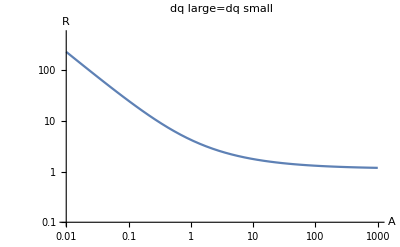

```mathematica
LogLogPlot[RSeL[A],{A,0.01,1000},AxesLabel->{"A","R"},PlotLabel->"dq large=dq small",GridLines->{{0.1,1}, {1, 10}},PlotRange->{0.1,500}]
```

```mathematica
Series[Sqrt[1+2x],{x,0,3}]
```

1+x-x^2/2+x^3/2+O[x]^4

```mathematica
Series[ArcTanh[x],{x,0,3}]
```

x+x^3/3+O[x]^4

```mathematica
(* Even solution of ODE with delta function souce *)
(* In this case p0+ = A/2 = - P0- *)
(* Kick by dP=A for t>0 *)
DeltaEven[q0_, A_,tmax_,color_,tk_]:=Delta[q0,-A/2,A,tmax,color,tk]
```

```mathematica
(* Phase portrait alone *)
P2Even[q_,q0_,A_]:=(A/2)^2+(q^2-q0^2)/2((q^2+q0^2)/2-1)
P2Even[q,q0,A]
```

A^2/4+1/2 (q^2-q0^2) (-1+1/2 (q^2+q0^2))

```mathematica
DeltaEvenPhase[q0_, A_,color_]:=Plot[{Re[Sqrt[P2Even[q,q0,A]]],-Re[Sqrt[P2Even[q,q0,A]]]},{q,-2(1+Abs[q0]),2(1+Abs[q0])},PlotStyle->color]
```

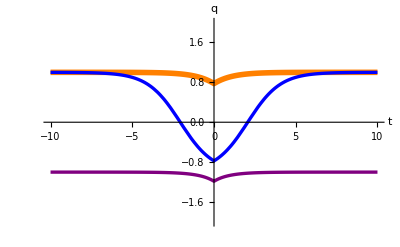

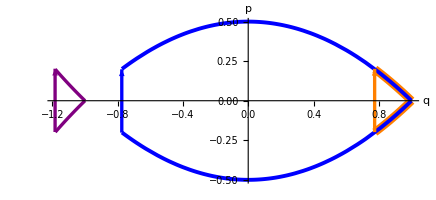

```mathematica
A0=0.4;
tmax0=10;
{ftc,fpc}=PlotFinite[A0,tmax0];
Show[ftc]
Show[fpc]
```

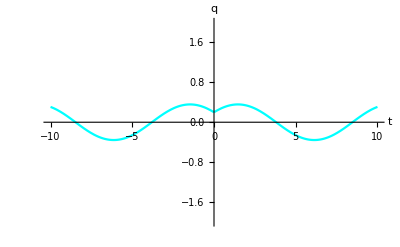

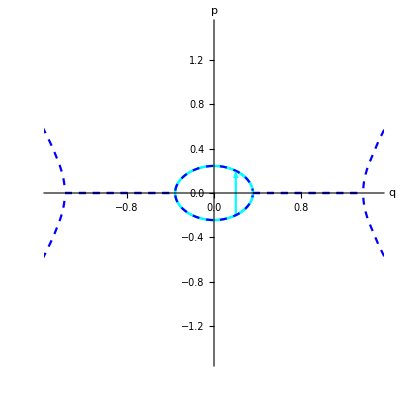

```mathematica
q02=0.2;
{ft2,fp2}=DeltaEven[q02,A0,tmax0,Cyan,0.004];
fpp2=DeltaEvenPhase[q02, A0,Directive[Blue,Dashed]];
Show[ft2]
Show[fp2,fpp2]
```

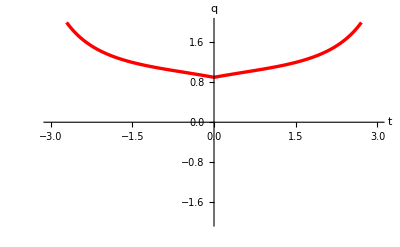

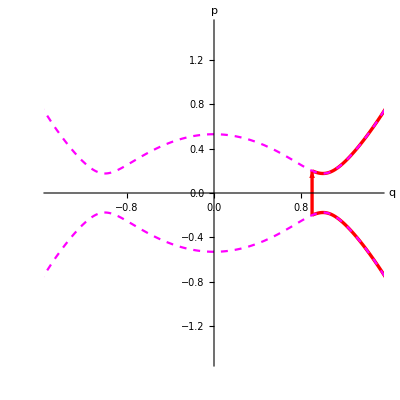

```mathematica
q01=0.9;
{ft1,fp1}=DeltaEven[q01,A0,3,Red,0.006];
fpp1=DeltaEvenPhase[q01, A0,Directive[Magenta,Dashed]];
Show[ft1]
Show[fp1,fpp1]
```

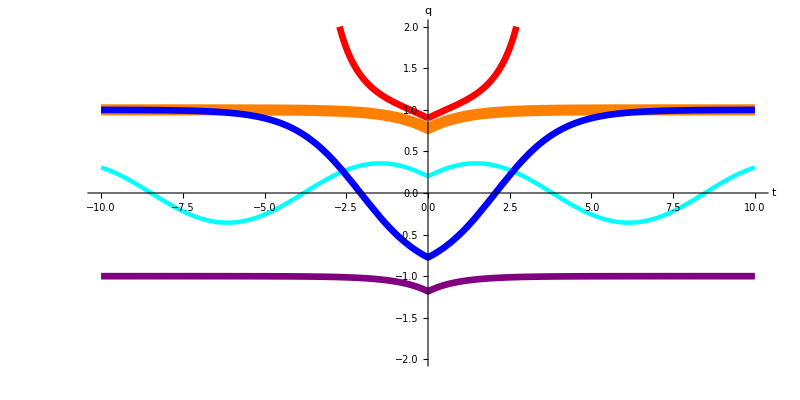

```mathematica
Show[ft2,ftc,ft1,ImageSize->800,AspectRatio->1/2]
```

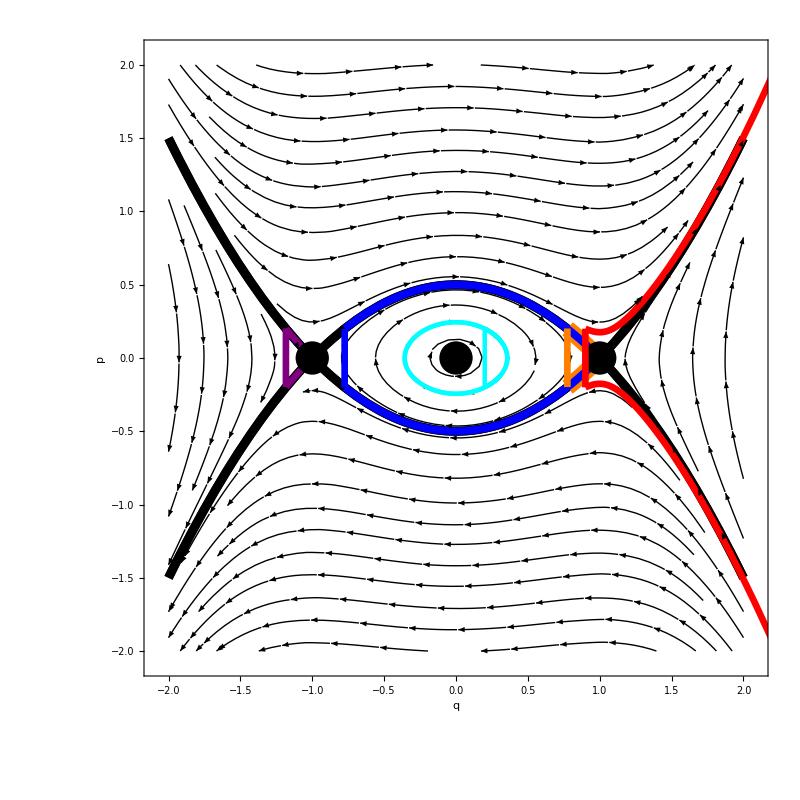

```mathematica
Show[s0,l0,fpc,fp2,fp1,ImageSize->800,AspectRatio->1]
```